```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Kinematic and Dynamic formulation of a planar 6-bar mechanism*)
```

```mathematica
(*Definitions*)
mf[x_]:=MatrixForm[x]
d[x_]:=Dimensions[x]
```

```mathematica
(*Robot*)
```

-Graphics-

```mathematica
(*Robot parameters*)
```

```mathematica
(*link lengths in mm, the radius of the link is taken to be 10mm*)
ldata = {l1->105,r1->75,h->210,r2->75,l2->105,b->210};
mdata = {m11->π*10^2*l1*0.0027,m12-> π*10^2*r1*0.0027,mb-> π*10^2*h*0.0027,m21-> π*10^2*l2*0.0027,m22-> π*10^2*r2*0.0027};
Idata = {IC11->m11*l1^2/12,IC12->m12*r1^2/12,ICb->mb*h^2/12,IC21->m21*l2^2/12,IC22->m22*r2^2/12};
```

```mathematica
(*The full configuration generalised coordinates*)
```

```mathematica
q = {ϕ1[t],θ3[t],θ1[t],ϕ2[t],θ2[t]};
```

```mathematica
(*Formulating the loop-closure equations*)
```

```mathematica
L1= {l1*Cos[ϕ1[t]],l1*Sin[ϕ1[t]]};
R1 = {r1*Cos[θ3[t]],r1*Sin[θ3[t]]};
H= {h*Cos[θ1[t]],h*Sin[θ1[t]]};
B = {b,0};
L2 = {l2*Cos[ϕ2[t]],l2*Sin[ϕ2[t]]};
R2 = {r2*Cos[θ2[t]],r2*Sin[θ2[t]]};
```

```mathematica
η = L1+R1+H-B-L2-R2;
```

```mathematica
Jηq = D[η,{q}];
```

```mathematica
(*The velocity Jacobians are*)
```

```mathematica
J11 = D[L1/2,{q}];
J12 = D[L1+R1/2,{q}];
Jb = D[L1+R1+H/2,{q}];
J21 = D[B+L2/2,{q}];
J22 = D[B+L2+R2/2,{q}];
```

```mathematica
Jω11 = {{0,0,0,0,0},{0,0,0,0,0},{1,0,0,0,0}};
Jω12 = {{0,0,0,0,0},{0,0,0,0,0},{0,1,0,0,0}};
Jωb   = {{0,0,0,0,0},{0,0,0,0,0},{0,0,1,0,0}};
Jω21 = {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,1,0}};
Jω22 = {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,1}};
```

```mathematica
(*Moment of Interias of the links*)
```

```mathematica
I11 = {{0,0,0}, {0,0,0}, {0, 0, IC11}};
I12 = {{0,0,0}, {0,0,0}, {0, 0, IC12}};
Ib   = {{0,0,0}, {0,0,0}, {0, 0, ICb}};
I21 = {{0,0,0}, {0,0,0}, {0, 0, IC21}};
I22 = {{0,0,0}, {0,0,0}, {0, 0, IC22}};
```

```mathematica
(*Mass matrix*)
```

```mathematica
M = Simplify[0.5*(m11*Transpose[J11].J11+m12*Transpose[J12].J12+mb*Transpose[Jb].Jb+m21*Transpose[J21].J21+m22*Transpose[J22].J22+Transpose[Jω11].I11.Jω11+Transpose[Jω12].I12.Jω12+Transpose[Jωb].Ib.Jωb+Transpose[Jω21].I21.Jω21+Transpose[Jω22].I22.Jω22)];
```

```mathematica
(*Verification of mass matrix symmetry*)
```

```mathematica
M-Transpose[M]//MatrixForm
```

(0. | 0 | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.)

```mathematica
mf[M/.Idata/.mdata/.ldata/.{θ1[t]->0,θ2[t]->2π/3,θ3[t]->π/3,ϕ1[t]-> 1.9360035480852633,ϕ2[t]-> 1.2055891055045298}]
```

(1.49628×10^6 | 521055. | -350690. | 0. | 0.
521055. | 560627. | 350690. | 0. | 0.
-350690. | 350690. | 1.30924×10^6 | 0. | 0.
0. | 0. | 0. | 514345. | 78947.8
0. | 0. | 0. | 78947.8 | 59641.2)

```mathematica
(*Computing the C matix from M matrix*)
```

```mathematica
n = Length[q];
tempC = Table[0, {ii, 1,n}, {jj, 1,n}];
For [ii = 1, ii ≤ n, 
For[jj = 1, jj ≤ n,
For[kk = 1, kk≤ n, 
tempC[[ii,jj]] +=1/2*( D[M[[ii,jj]], q[[kk]]] + D[M[[ii,kk]], q[[jj]]] - D[M[[jj, kk]], q[[ii]]])*D[q[[kk]],t] ;
kk++];
jj++];
ii++];
```

```mathematica
Cmat = FullSimplify[tempC];
```

```mathematica
(*Verifying the property of Cmat*)
```

```mathematica
A = FullSimplify[D[M,t]-2*Cmat];
mf[Simplify[A+Transpose[A]]]
```

(0. | 0. | 0. | 0 | 0
0. | 0. | 0. | 0 | 0
0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0. | 0.
0 | 0 | 0 | 0. | 0.)

```mathematica
(*Potential gradient*)
```

```mathematica
PE = (m11*(L1[[2]]/2)*g+m12*(L1+R1/2)[[2]]*g+mb*(L1+R1+H/2)[[2]]*g+m21*(B+L2/2)[[2]]*g+m22*(B+L2+R2/2)[[2]]*g)/.g->9.806;
```

```mathematica
PE/.Idata/.mdata/.ldata
```

45851.6 Sin[ϕ1[t]]+623.831 (75/2 Sin[θ3[t]]+105 Sin[ϕ1[t]])+1746.73 (105 Sin[θ1[t]]+75 Sin[θ3[t]]+105 Sin[ϕ1[t]])+45851.6 Sin[ϕ2[t]]+623.831 (75/2 Sin[θ2[t]]+105 Sin[ϕ2[t]])

```mathematica
G = D[PE,{q}];
```

```mathematica
(*Now formulating the constraint force term*)
```

```mathematica
tempA = Inverse[Jηq.Inverse[M].Transpose[Jηq]/.Idata/.mdata/.ldata];
d[tempA]
```

{2,2}

```mathematica
tempA/.{θ1[t]->0,θ2[t]->2π/3,θ3[t]->π/3,ϕ1[t]-> 1.9360035480852633,ϕ2[t]-> 1.2055891055045298}
```

{{16.5649,-8.30183},{-8.30183,16.7025}}

```mathematica
tempB= D[Jηq,t].D[q,t]/.Idata/.mdata/.ldata;
```

```mathematica
(*The unconstrained acceleration*)
```

```mathematica
a = Inverse[M].(0-Cmat.D[q,t]-G);
d[a]
```

{5}

```mathematica
tempD = Jηq.a;
d[tempD]
```

{2}

```mathematica
(*Computing λ*)
```

```mathematica
λ =-tempA.(tempB+tempD);
```

```mathematica
(*From this the constrained Lagrangian term of the RHS will be*)
```

```mathematica
eqnofmRHS = Transpose[Jηq].λ/.Idata/.mdata/.ldata;
d[eqnofmRHS]
```

{5}

```mathematica
eqnofmLHS = M.D[q,{t,2}]+Cmat.D[q,t]+G/.Idata/.mdata/.ldata;
d[eqnofmLHS]
```

{5}

```mathematica
(*Therefore the complete equation of motion is*)
```

```mathematica
eqnofm = eqnofmLHS-eqnofmRHS;
d[eqnofm]
Variables[eqnofm]
```

{5}

{Cos[θ1[t]],Cos[θ2[t]],Cos[θ1[t]-θ3[t]],Cos[θ3[t]],Cos[θ1[t]-ϕ1[t]],Cos[θ3[t]-ϕ1[t]],Cos[ϕ1[t]],Cos[θ2[t]-ϕ2[t]],Cos[ϕ2[t]],Sin[θ1[t]],Sin[θ2[t]],Sin[θ1[t]-θ3[t]],Sin[θ3[t]],Sin[θ1[t]-ϕ1[t]],Sin[θ3[t]-ϕ1[t]],Sin[ϕ1[t]],Sin[θ2[t]-ϕ2[t]],Sin[ϕ2[t]],θ1'[t],θ2'[t],θ3'[t],ϕ1'[t],ϕ2'[t],θ1''[t],θ2''[t],θ3''[t],ϕ1''[t],ϕ2''[t]}

```mathematica
(*Initial pose*)
```

```mathematica
{θ1[0]->0,θ2[0]->2π/3,θ3[0]->π/3,ϕ1[0]-> 1.9360035480852633,ϕ2[0]-> 1.2055891055045298}
```

{θ1[0]→0,θ2[0]→(2 π)/3,θ3[0]→π/3,ϕ1[0]→1.936,ϕ2[0]→1.20559}

```mathematica
N[Solve[(η/.{θ1[t]->0,θ2[t]->2π/3,θ3[t]->π/3}/.ldata)==0,{ϕ1[t],ϕ2[t]}]]
```

{{ϕ1[t]→ConditionalExpression[1.936+6.28319 C[1],C[1]∈ℤ],ϕ2[t]→ConditionalExpression[1.20559+6.28319 C[2],C[2]∈ℤ]},{ϕ1[t]→ConditionalExpression[-1.936+6.28319 C[1],C[1]∈ℤ],ϕ2[t]→ConditionalExpression[-1.20559+6.28319 C[2],C[2]∈ℤ]}}

```mathematica
(*Simulating the 6 bar system using NDSolve*)
```

```mathematica
sol = NDSolve[{eqnofm[[1]]==0,eqnofm[[2]]==0,eqnofm[[3]]==0,eqnofm[[4]]==0,eqnofm[[5]]==0,θ1[0]==0,θ2[0]==2π/3,θ3[0]==π/3,ϕ1[0]==1.9360035480852633,ϕ2[0]==1.2055891055045298,θ1'[0]==0,θ2'[0] == 0,θ3'[0]==0,ϕ1'[0] == 0,ϕ2'[0] == 0},{θ1,θ2,θ3,ϕ1,ϕ2},{t,0,60},Method-> {"EquationSimplification"->"Residual"}]
(*Method->{"EquationSimplification"->"Residual"}*)
```

{{θ1→InterpolatingFunction[…],θ2→InterpolatingFunction[…],θ3→InterpolatingFunction[…],ϕ1→InterpolatingFunction[…],ϕ2→InterpolatingFunction[…]}}

```mathematica
(*Plotting joint angles*)
```

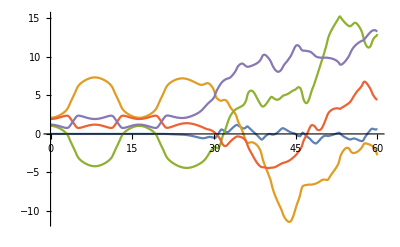

```mathematica
Plot[Evaluate[{θ1[t],θ2[t],θ3[t],ϕ1[t],ϕ2[t]}/.sol],{t,0,60}]
```

```mathematica
(*Now verifying the energy*)
```

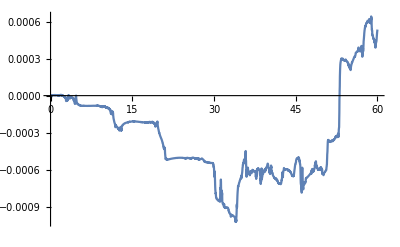

```mathematica
H = (PE+0.5*D[q,t].M.D[q,t])/.Idata/.mdata/.ldata;
δH = (H/(H/.{t->0})-1)*100;
Plot[δH/.sol,{t,0,60}]
```

```mathematica
θ1temp =  θ1[t]/.sol;
θ1data =ConstantArray[0,6001];
i=1;
For [time=0,time≤60,time = time+0.01,
θ1data[[i]] = θ1temp[[1]]/.t->time;
i ++;
];
θ2temp = θ2[t]/.sol;
θ2data = ConstantArray[0,6001];
i=1;
For [time=0,time<=60,time = time+0.01,
θ2data[[i]] = θ2temp[[1]]/.t->time;
i ++;
];
θ3temp = θ3[t]/.sol;
θ3data = ConstantArray[0,6001];
i=1;
For [time=0,time<=60,time = time+0.01,
θ3data[[i]] = θ3temp[[1]]/.t->time;
i ++;
];
ϕ1temp = ϕ1[t]/.sol;
ϕ1data = ConstantArray[0,6001];
i=1;
For [time=0,time<=60,time = time+0.01,
ϕ1data[[i]] = ϕ1temp[[1]]/.t->time;
i ++;
];
ϕ2temp = ϕ2[t]/.sol;
ϕ2data = ConstantArray[0,6001];
i=1;
For [time=0,time<=60,time = time+0.01,
ϕ2data[[i]] = ϕ2temp[[1]]/.t->time;
i ++;
];
(*Export["t1data.csv",θ1data]*)
```

```mathematica
(*The torques are the control inputs u1,u2,u3*)
```

```mathematica
τ = {0,u3[t],u1[t],0,u2[t]};
```

```mathematica
eqnofmτ = eqnofm-τ;
```

```mathematica
ddots = Solve[eqnofmτ==0,{θ1''[t],θ2''[t],θ3''[t],ϕ1''[t],ϕ2''[t]}]
```